```mathematica
x[a_,t_]:=a(t-Sin[t]);
y[a_,t_]:=a(1-Cos[t]);
circlecolor=RGBColor[0.7,0.7,0.7];
```

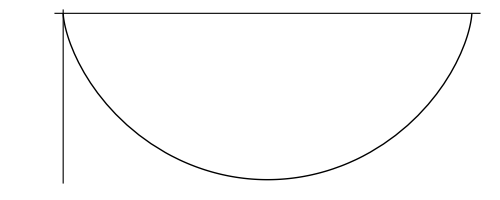

```mathematica
pp=ParametricPlot[{x[1,t],-y[1,t]},{t,0,2Pi},Ticks->None,PlotStyle->{Black,Thick}]
```

```mathematica
Animate[Show[pp,Graphics[{Disk[{x[1,t],-y[1,t]},0.07],{circlecolor,{Line[{{t,-1},{x[1,t],-y[1,t]}}],Circle[{t,-1}]}}}]],{t,0,2Pi}]
```

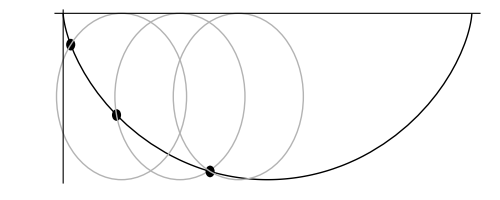

```mathematica
Apply[Show,Join[{pp},Table[Graphics[{Disk[{x[1,t],-y[1,t]},0.07],{circlecolor,Circle[{t,-1}]}}],{t,2Pi/7,2Pi*3/7,2Pi/7}]]]
```